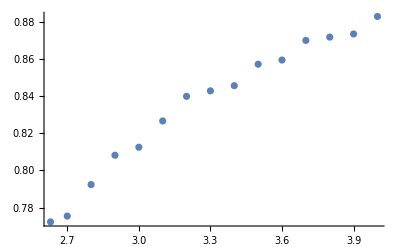

```mathematica
a={{2.63,65/(2.63×32)},{2.7,67/(2.7×32)},{2.8,71/(2.8×32)},{2.9,75/(2.9×32)},{3.0,78/(3.0×32)},{3.1,82/(3.1×32)},{3.2,86/(3.2×32)},{3.3,89/(3.3×32)},{3.4,92/(3.4×32)},{3.5,96/(3.5×32)}, {3.6,99/(3.6×32)},{3.7,103/(3.7×32)},{3.8,106/(3.8×32)}, {3.9,109/(3.9×32)},{4.0,113/(4×32)}};
ListPlot[{a}]
```

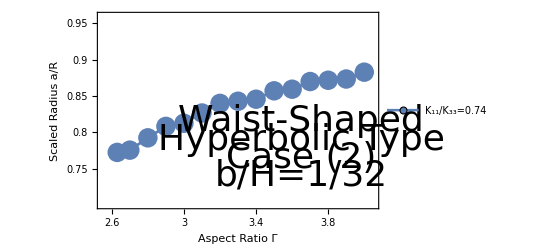

```mathematica
ListPlot[{a},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.75,0.80,0.85,0.9,0.95},None},{{2.6,2.8,3,3.2,3.4,3.6,3.8,4},None}}, PlotRange->{{2.55,4.05},{0.7,0.96}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.74","K_11/K_33=2.0","K_11/K_33=3.0","K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Top}],Epilog->{Text[Style["Waist-Shaped",Directive[Black,36]],{3.65,0.815}],Text[Style["Hyperbolic Type",Directive[Black,36]],{3.65,0.79}],Text[Style["Case (2)",Directive[Black,36]],{3.65,0.765}],Text[Style["b/H=1/32",Directive[Black,36]],{3.65,0.74}]}]
```